```mathematica
f[x_]:=(1-(x^2-xmu2)/((x x-xmu2)^2+xdt2)^(1/2))x x;
```

```mathematica
f[x]
```

x^2 (1-(x^2-xmu2)/(√(xdt2+(x^2-xmu2)^2)))

```mathematica
NIntegrate[f[x]/.{xmu2->1,xdt2->0.0001},{x,0,Infinity}]
```

0.666846

```mathematica
N[%]
```

0.666846

```mathematica
FindRoot[NIntegrate[(f[x]/.{xmu2->0.9}),{x,0,Infinity}]==2/3,{xdt2,0.1}]
```

NIntegrate::inumr: The integrand x^2\ (1 - -0.9 + x^2/√(-0.9 + Power[« 2 »])^2 + xdt2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

FindRoot::jsing: Encountered a singular Jacobian at the point {xdt2} = {0.1}. Try perturbing the initial point(s).

{xdt2→0.1}

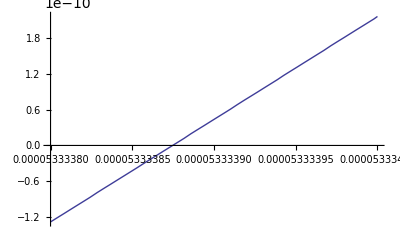

```mathematica
Plot[NIntegrate[(f[x]/.{xmu2->0.9999}),{x,0,Infinity}]-2/3,{xdt2,0.0000533338,0.000053334}]
```

```mathematica
N[8Pi^3/3]
```

82.6834

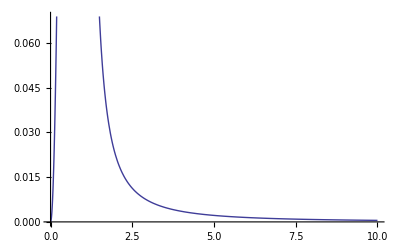

```mathematica
Plot[f[x]/.{xmu2->0.99,xdt2->0.1},{x,0,10}]
```

```mathematica
muDtL={{0.9999,0.00005333385},{0.999,0.00064},{0.99,0.0079665},{0.97,0.0269707},{0.95,0.0476463},{0.94,0.05837507},{0.93,0.0693001},{0.9,0.10298},{0.8,0.2205},{0.7,0.34},{0.6,0.46005},{0.5,.577},{.3,.8005},{.1,1.01},{0,1.107},{-0.1,1.2},{-0.3,1.38},{-.5,1.545},{-.7,1.7},{-.9,1.854},{-1,1.915},{-1.5,2.24},{-2,2.525},{-2.5,2.785},{-3,3.02},{-4,3.46},{-5,3.85},{-6,4.2},{-8,4.85},{-10,5.395},{-15,6.593},{-20,7.6056},{-30,9.307}}
```

{{0.9999,0.0000533339},{0.999,0.00064},{0.99,0.0079665},{0.97,0.0269707},{0.95,0.0476463},{0.94,0.0583751},{0.93,0.0693001},{0.9,0.10298},{0.8,0.2205},{0.7,0.34},{0.6,0.46005},{0.5,0.577},{0.3,0.8005},{0.1,1.01},{0,1.107},{-0.1,1.2},{-0.3,1.38},{-0.5,1.545},{-0.7,1.7},{-0.9,1.854},{-1,1.915},{-1.5,2.24},{-2,2.525},{-2.5,2.785},{-3,3.02},{-4,3.46},{-5,3.85},{-6,4.2},{-8,4.85},{-10,5.395},{-15,6.593},{-20,7.6056},{-30,9.307}}

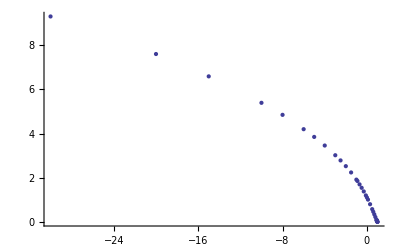

```mathematica
ListPlot[muDtL]
```

```mathematica
f1[x_]:=(x x)/((x x-xmu2)^2+xdt4)^(1/2)-1
```

```mathematica
f1[x]
```

-1+x^2/(√(xdt4+(x^2-xmu2)^2))

```mathematica
f1[x]mu{xmu2->1,xdt4->2}
```

{mu (-1+x^2/(√(xdt4+(x^2-xmu2)^2))) (xmu2→1),mu (-1+x^2/(√(xdt4+(x^2-xmu2)^2))) (xdt4→2)}

```mathematica
length=Length[muDtL];intact={};
For[i=1,i≤length,i++,
strength=2/Pi NIntegrate[f1[x]/.{xmu2->muDtL[[i,1]],xdt4->muDtL[[i,2]]},{x,0,Infinity}];intact=Append[intact,strength]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99228}. NIntegrate obtained 4.99858 and 0.0000122024 for the integral and error estimates.

```mathematica
intact
```

{3.1822,2.38973,1.5756,1.16658,0.967024,0.893712,0.830707,0.680721,0.367452,0.166638,0.0128024,-0.113235,-0.316811,-0.481182,-0.553235,-0.620286,-0.742788,-0.852479,-0.952547,-1.04524,-1.08865,-1.28824,-1.46346,-1.6213,-1.76587,-2.02578,-2.25686,-2.46689,-2.84159,-3.17281,-3.88003,-4.47743,-5.48076}

```mathematica
muL=Transpose[muDtL][[1]];dtL=Transpose[muDtL][[2]]^(1/2);
```

```mathematica
muL
```

{0.9999,0.999,0.99,0.97,0.95,0.94,0.93,0.9,0.8,0.7,0.6,0.5,0.3,0.1,0,-0.1,-0.3,-0.5,-0.7,-0.9,-1,-1.5,-2,-2.5,-3,-4,-5,-6,-8,-10,-15,-20,-30}

```mathematica
Transpose[{intact,muL}]
```

{{3.1822,0.9999},{2.38973,0.999},{1.5756,0.99},{1.16658,0.97},{0.967024,0.95},{0.893712,0.94},{0.830707,0.93},{0.680721,0.9},{0.367452,0.8},{0.166638,0.7},{0.0128024,0.6},{-0.113235,0.5},{-0.316811,0.3},{-0.481182,0.1},{-0.553235,0},{-0.620286,-0.1},{-0.742788,-0.3},{-0.852479,-0.5},{-0.952547,-0.7},{-1.04524,-0.9},{-1.08865,-1},{-1.28824,-1.5},{-1.46346,-2},{-1.6213,-2.5},{-1.76587,-3},{-2.02578,-4},{-2.25686,-5},{-2.46689,-6},{-2.84159,-8},{-3.17281,-10},{-3.88003,-15},{-4.47743,-20},{-5.48076,-30}}

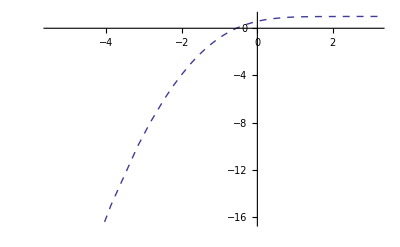

```mathematica
muPlot=ListLinePlot[Transpose[{intact, muL}],PlotStyle->Dashed]
```

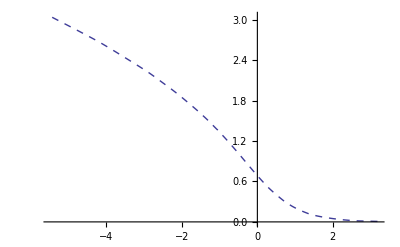

```mathematica
dtPlot=ListLinePlot[Transpose[{intact,dtL}],InterpolationOrder->2,PlotStyle->Dashed]
```

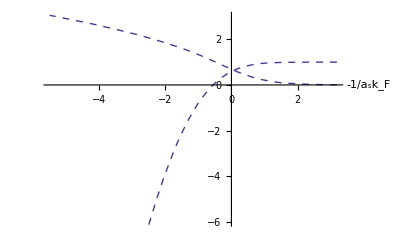

```mathematica
Show[dtPlot,muPlot,AxesLabel->{"-1/a_sk_F",""},AxesOrigin->{0,0},LabelStyle->Directive[Bold,Larger], PlotRange->{-6,3}]
```

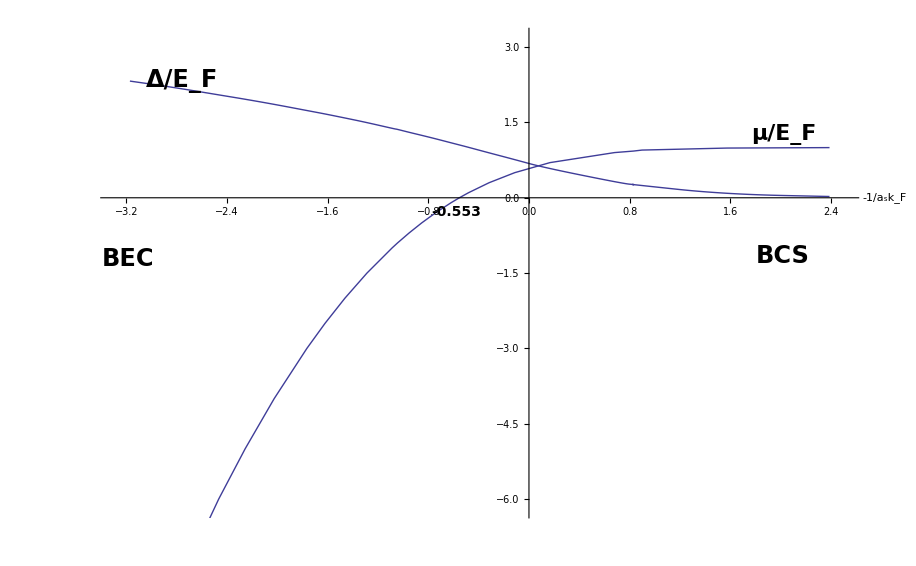

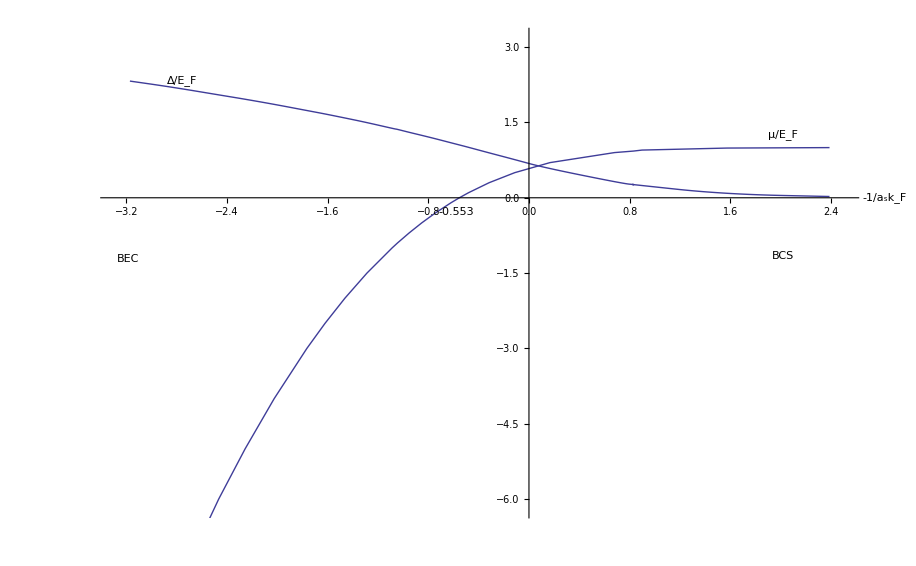

```mathematica
alpha2=3*2^(1/2)*dtL^2/(128*(dtt *2)^(1/2))
```

{(1.25001×10^-6)/(√dtt),0.000015/(√dtt),0.000186715/(√dtt),0.000632126/(√dtt),0.00111671/(√dtt),0.00136817/(√dtt),0.00162422/(√dtt),0.00241359/(√dtt),0.00516797/(√dtt),0.00796875/(√dtt),0.0107824/(√dtt),0.0135234/(√dtt),0.0187617/(√dtt),0.0236719/(√dtt),0.0259453/(√dtt),0.028125/(√dtt),0.0323438/(√dtt),0.0362109/(√dtt),0.0398438/(√dtt),0.0434531/(√dtt),0.0448828/(√dtt),0.0525/(√dtt),0.0591797/(√dtt),0.0652734/(√dtt),0.0707813/(√dtt),0.0810938/(√dtt),0.0902344/(√dtt),0.0984375/(√dtt),0.113672/(√dtt),0.126445/(√dtt),0.154523/(√dtt),0.178256/(√dtt),0.218133/(√dtt)}

```mathematica
weight=1/(1+alpha2)^(2/3);shiftIntact=intact*(weight)^(1/2)+muL*2;intactShift=(shiftIntact*weight^(1/2));intactShift=((intact*weight^(1/2))+2muL*(weight))*weight^(-1/2);
```

```mathematica
intactSt2=intact*(2*30)^(1/2)+muL*2
```

{26.649,20.5087,14.1845,10.9763,9.39053,8.80266,8.29463,7.07284,4.44627,2.69077,1.29917,0.122885,-1.85401,-3.52722,-4.28534,-5.00472,-6.35361,-7.60327,-8.7784,-9.89641,-10.4326,-12.9787,-15.3359,-17.5585,-19.6784,-23.6916,-27.4816,-31.1084,-38.0109,-44.5765,-60.0546,-74.682,-102.454}

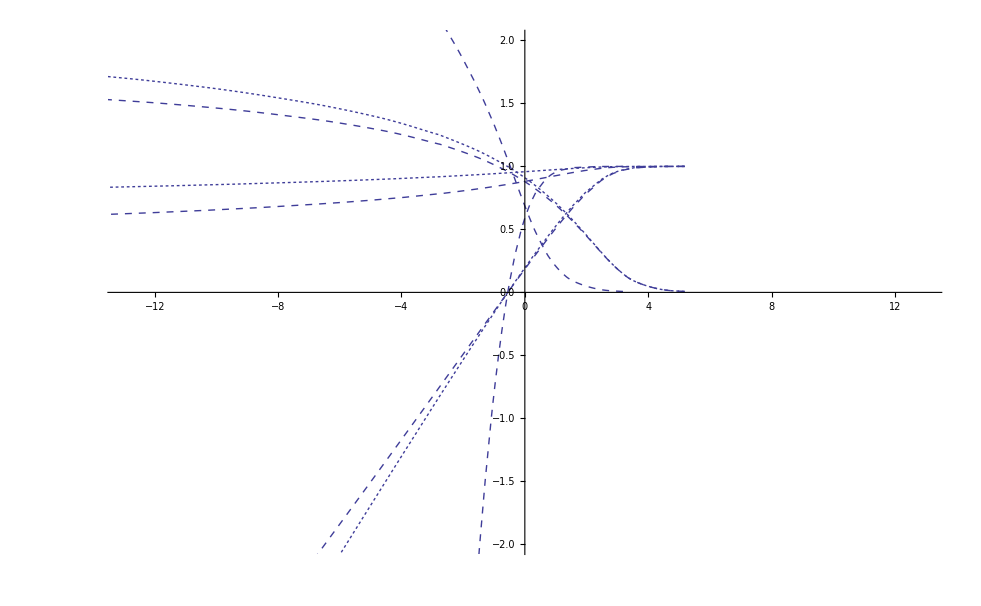

```mathematica
muPlotSt=ListLinePlot[Transpose[{intactShift,muL*weight}]/.{dtt->0.01},PlotStyle->{Dashed}];
wPlot=ListLinePlot[Transpose[{intactShift,weight}]/.{dtt->.01},PlotStyle->{Dashed}];
dtPlotSt=ListLinePlot[Transpose[{intactShift,dtL*weight}]/.{dtt->.03},InterpolationOrder->2,PlotStyle->{Dashed}];
muPlotSt2=ListLinePlot[Transpose[{intactShift, muL*weight}]/.{dtt->0.1},PlotStyle->{Dashing[Tiny]}];dtPlotSt2=ListLinePlot[Transpose[{intactShift,dtL*weight}]/.{dtt->0.1},InterpolationOrder->2,PlotStyle->{Dashing[Tiny]}];
wPlotSt2=ListLinePlot[Transpose[{intactShift,weight}]/.{dtt->.1},PlotStyle->{Dashing[Tiny]}];
Show[dtPlotSt,muPlotSt,dtPlot,wPlot,muPlot,muPlotSt2,dtPlotSt2,wPlotSt2,AxesOrigin->{0,0},LabelStyle->Directive[Bold,Larger], PlotRange->{{-13,13},{-2,2}}]
```

```mathematica
ListLinePlot[Transpose[{intactShift, muL*weight}]/.{dtt->0.1.08}]
```

-Graphics-

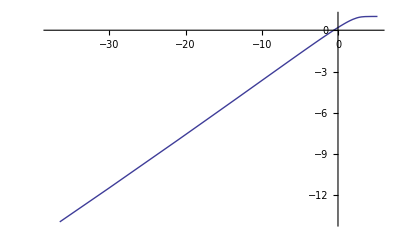

```mathematica
ListLinePlot[Transpose[{intactShift,muL*weight}]/.{dtt->0.1}]
```

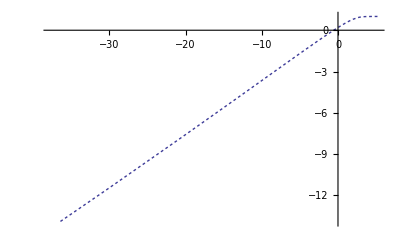

```mathematica
ListLinePlot[Transpose[{intactShift, muL*weight}]/.{dtt->0.1},PlotStyle->{Dashing[Tiny]}]
```

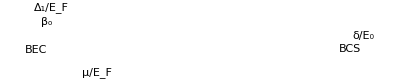
```mathematica
symbol=-Graphics-;
```

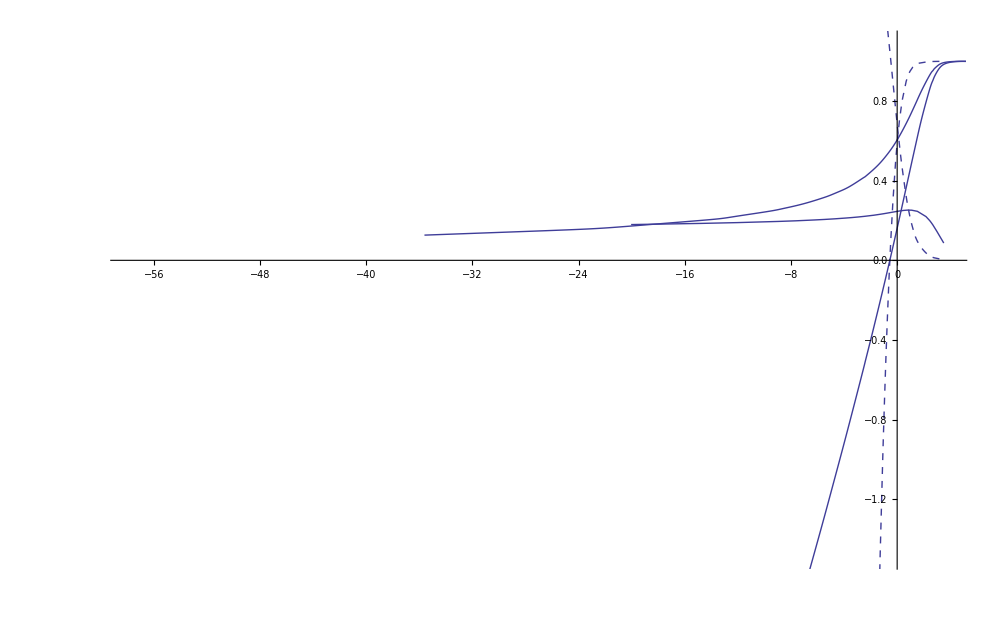

```mathematica
muPlotSt3=ListLinePlot[Transpose[{intactShift,muL*weight}]/.{dtt->0.001},InterpolationOrder->3];
muPlotSt4=ListLinePlot[Transpose[{intactShift*weight^(-1/2),muL*weight}]/.{dtt->0.001},InterpolationOrder->3];
wPlot3=ListLinePlot[Transpose[{intactShift,weight^(3/2)}]/.{dtt->.001},InterpolationOrder->5];
dtPlotSt3=ListLinePlot[Transpose[{intactShift,dtL*weight}]/.{dtt->.001}];Show[dtPlotSt3,muPlotSt3,wPlot3,muPlot,dtPlot,AxesOrigin->{0,0},LabelStyle->Directive[Bold,Larger], PlotRange->{{-58,4},{-1.5,1.1}}]
```

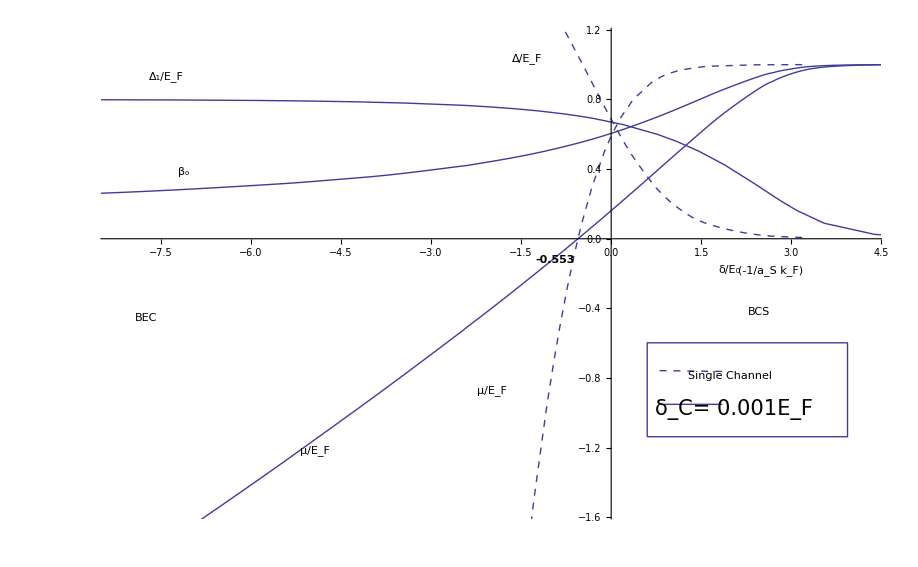
```mathematica
narrowPlotNew001=-Graphics-;
```

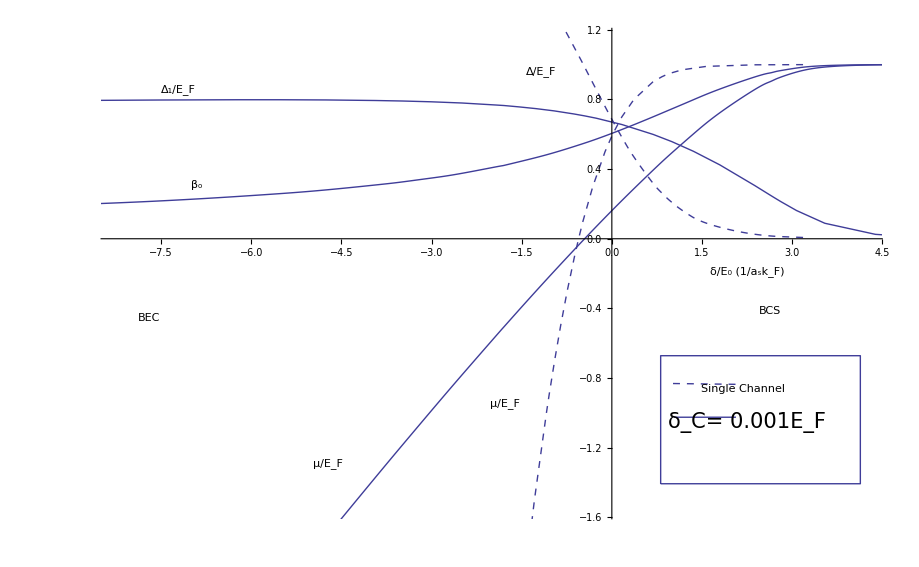

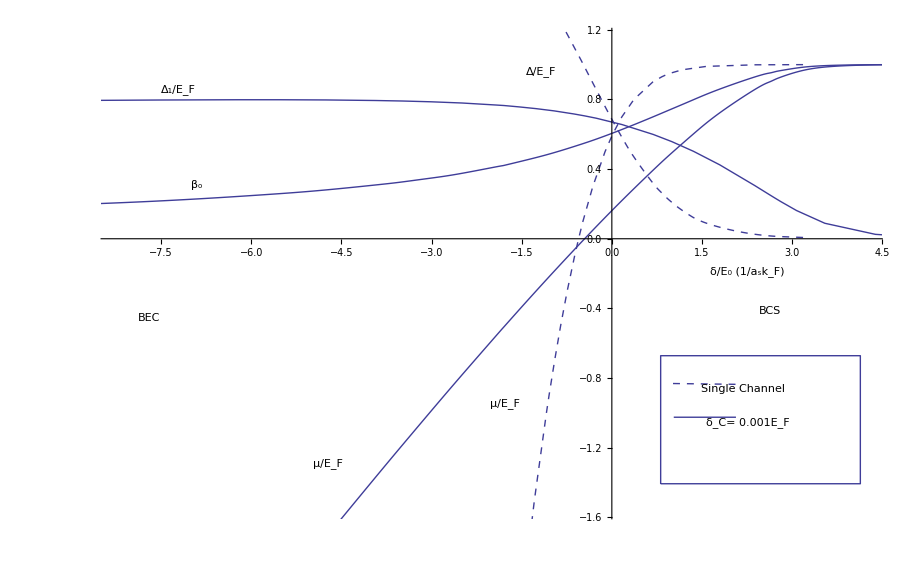

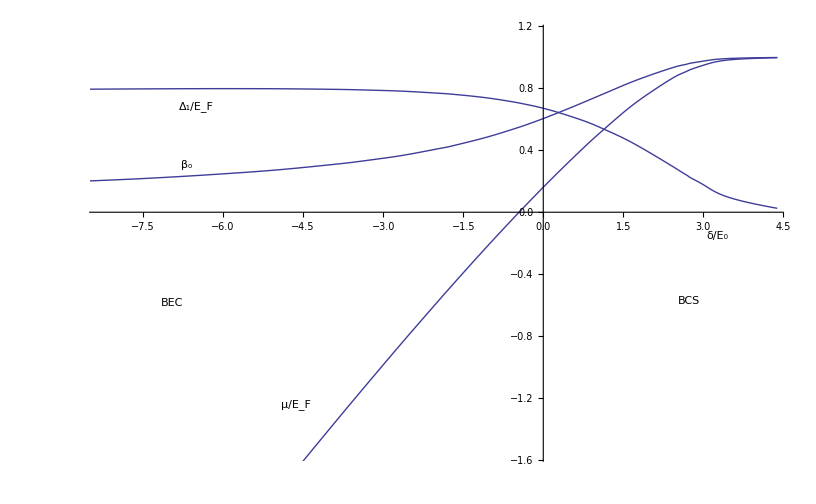
```mathematica
narrowPlot001=-Graphics-;
```

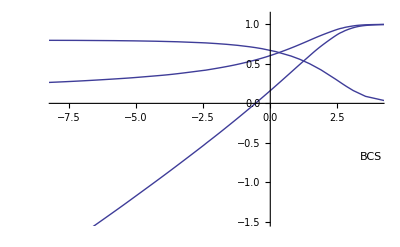

```mathematica
Show[dtPlotSt3,muPlotSt3,wPlot3,symbol,AxesOrigin->{0,0},LabelStyle->Directive[Bold,Larger], PlotRange->{{-8,4},{-1.5,1.1}}]
```

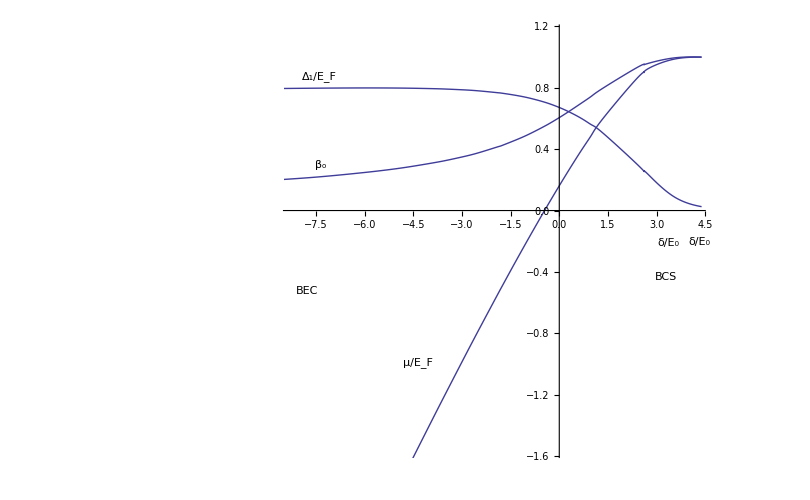
```mathematica
narrow001=-Graphics-;
```

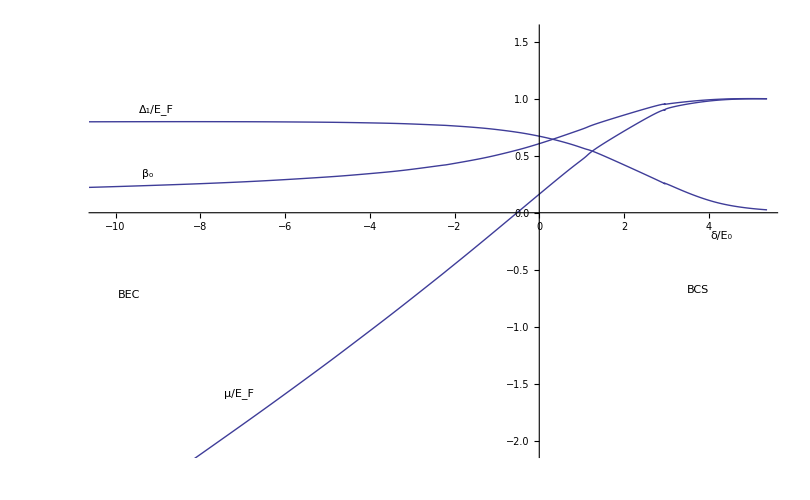

-Graphics-

-Graphics-

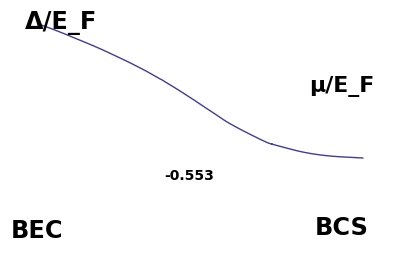
```mathematica
s=-Graphics-
```

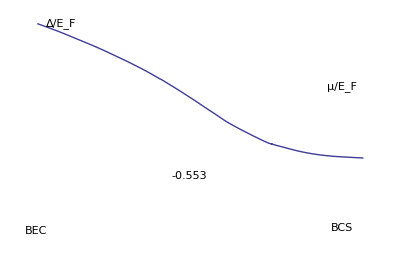

```mathematica
muDtL[[1]]
```

{0.9999,0.0000533339}

```mathematica
Length[muDtL]
```

33

```mathematica
a=0;a=
```

ListLinePlot::ioproc: {{1.9998  + 3.1822/(1 + 1.25001×10^-6\ Power[« 2 »])^1/3, 0.007303}, {1.998  + 2.38973/(1 + 0.000015\ Power[« 2 »])^1/3, 0.0252982}, {1.98  + 1.5756/(1 + 0.000186715\ Power[« 2 »])^1/3, 0.0892553}, {1.94  + 1.16658/(1 + 0.000632126\ Power[« 2 »])^1/3, 0.164228}, « 26 », {-30 - 3.88003/(1 + 0.154523\ Power[« 2 »])^1/3, 2.56768}, {-40 - 4.47743/(1 + 0.178256\ Power[« 2 »])^1/3, 2.75783}, {-60 - 5.48076/(1 + 0.218133\ Power[« 2 »])^1/3, 3.05074}}
 may contain non-machine precision numbers, complex numbers, or invalid entries.

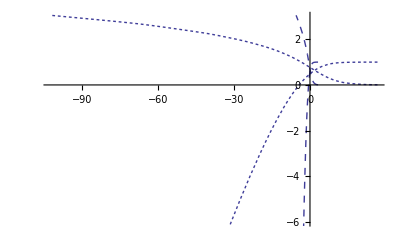

```mathematica
muPlotSt=ListLinePlot[Transpose[{shiftIntact, muL}],PlotStyle->{Dashed}];dtPlotSt=ListLinePlot[Transpose[{shiftIntact,dtL}],InterpolationOrder->2,PlotStyle->{Dashed}];
muPlotSt2=ListLinePlot[Transpose[{intactSt2, muL}],PlotStyle->{Dashing[Tiny]}];dtPlotSt2=ListLinePlot[Transpose[{intactSt2,dtL}],InterpolationOrder->2,PlotStyle->{Dashing[Tiny]}];
Show[dtPlotSt,muPlotSt,dtPlot,muPlot,muPlotSt2,dtPlotSt2,AxesOrigin->{0,0},LabelStyle->Directive[Bold,Larger], PlotRange->{-6,3}]
```

```mathematica
Transpose[{intactShift,weight}]/.{dtt->0.1}
```

{{5.18199,0.999997},{4.3877,0.999968},{3.55521,0.999607},{3.10528,0.99867},{2.86479,0.997653},{2.77101,0.997126},{2.68753,0.99659},{2.47616,0.994944},{1.95883,0.989251},{1.55507,0.983545},{1.19947,0.977896},{0.872903,0.972469},{0.271772,0.962305},{-0.285937,0.953015},{-0.553235,0.948789},{-0.814686,0.944781},{-1.32362,0.937142},{-1.81699,0.930274},{-2.29825,0.923936},{-2.76962,0.917744},{-3.00209,0.915321},{-4.13851,0.902671},{-5.24114,0.891931},{-6.31813,0.882408},{-7.3752,0.874016},{-9.43961,0.858826},{-11.4542,0.845902},{-13.4304,0.834709},{-17.2848,0.814871},{-21.0515,0.799119},{-30.1539,0.767018},{-38.9396,0.742276},{-55.8548,0.704872}}

```mathematica
weight/.{dtt->0.001}
```

{0.999974,0.999684,0.996083,0.986892,0.977129,0.972158,0.96716,0.952148,0.904012,0.860859,0.822345,0.788713,0.733053,0.688987,0.670726,0.654313,0.625218,0.601224,0.580673,0.561909,0.554887,0.520864,0.494996,0.474019,0.456866,0.428557,0.406848,0.389556,0.361826,0.342061,0.306735,0.283153,0.252149}

```mathematica
weight
```

{1/((1+(1.25001×10^-6)/(√dtt))^(2/3)),1/(1+0.000015/(√dtt))^(2/3),1/(1+0.000186715/(√dtt))^(2/3),1/(1+0.000632126/(√dtt))^(2/3),1/(1+0.00111671/(√dtt))^(2/3),1/(1+0.00136817/(√dtt))^(2/3),1/(1+0.00162422/(√dtt))^(2/3),1/(1+0.00241359/(√dtt))^(2/3),1/(1+0.00516797/(√dtt))^(2/3),1/(1+0.00796875/(√dtt))^(2/3),1/(1+0.0107824/(√dtt))^(2/3),1/(1+0.0135234/(√dtt))^(2/3),1/(1+0.0187617/(√dtt))^(2/3),1/(1+0.0236719/(√dtt))^(2/3),1/(1+0.0259453/(√dtt))^(2/3),1/(1+0.028125/(√dtt))^(2/3),1/(1+0.0323438/(√dtt))^(2/3),1/(1+0.0362109/(√dtt))^(2/3),1/(1+0.0398438/(√dtt))^(2/3),1/(1+0.0434531/(√dtt))^(2/3),1/(1+0.0448828/(√dtt))^(2/3),1/(1+0.0525/(√dtt))^(2/3),1/(1+0.0591797/(√dtt))^(2/3),1/(1+0.0652734/(√dtt))^(2/3),1/(1+0.0707813/(√dtt))^(2/3),1/(1+0.0810938/(√dtt))^(2/3),1/(1+0.0902344/(√dtt))^(2/3),1/(1+0.0984375/(√dtt))^(2/3),1/(1+0.113672/(√dtt))^(2/3),1/(1+0.126445/(√dtt))^(2/3),1/(1+0.154523/(√dtt))^(2/3),1/(1+0.178256/(√dtt))^(2/3),1/(1+0.218133/(√dtt))^(2/3)}

```mathematica
alpha2/.{dtt->0.01}
```

{0.0000125001,0.00015,0.00186715,0.00632126,0.0111671,0.0136817,0.0162422,0.0241359,0.0516797,0.0796875,0.107824,0.135234,0.187617,0.236719,0.259453,0.28125,0.323438,0.362109,0.398438,0.434531,0.448828,0.525,0.591797,0.652734,0.707813,0.810938,0.902344,0.984375,1.13672,1.26445,1.54523,1.78256,2.18133}

```mathematica
alpha2
```

{(1.25001×10^-6)/(√dtt),0.000015/(√dtt),0.000186715/(√dtt),0.000632126/(√dtt),0.00111671/(√dtt),0.00136817/(√dtt),0.00162422/(√dtt),0.00241359/(√dtt),0.00516797/(√dtt),0.00796875/(√dtt),0.0107824/(√dtt),0.0135234/(√dtt),0.0187617/(√dtt),0.0236719/(√dtt),0.0259453/(√dtt),0.028125/(√dtt),0.0323438/(√dtt),0.0362109/(√dtt),0.0398438/(√dtt),0.0434531/(√dtt),0.0448828/(√dtt),0.0525/(√dtt),0.0591797/(√dtt),0.0652734/(√dtt),0.0707813/(√dtt),0.0810938/(√dtt),0.0902344/(√dtt),0.0984375/(√dtt),0.113672/(√dtt),0.126445/(√dtt),0.154523/(√dtt),0.178256/(√dtt),0.218133/(√dtt)}

```mathematica
dtL
```

{0.007303,0.0252982,0.0892553,0.164228,0.21828,0.241609,0.263249,0.320905,0.469574,0.583095,0.67827,0.759605,0.894707,1.00499,1.05214,1.09545,1.17473,1.24298,1.30384,1.36162,1.38384,1.49666,1.58902,1.66883,1.73781,1.86011,1.96214,2.04939,2.20227,2.32271,2.56768,2.75783,3.05074}

```mathematica
dtL*weight/.{dtt->.001}
```

{0.00730281,0.0252902,0.0889056,0.162075,0.213288,0.234882,0.254604,0.305549,0.424501,0.501963,0.557772,0.599111,0.655867,0.692424,0.705699,0.716764,0.734465,0.74731,0.757105,0.765105,0.767872,0.779558,0.786561,0.791058,0.793948,0.797162,0.798294,0.798353,0.79684,0.79451,0.787599,0.780886,0.769239}

```mathematica
Transpose[{intactShift,dtL*weight}]/.{dtt->.001}
```

{{5.18197,0.00730281},{4.38741,0.0252902},{3.55172,0.0889056},{3.09382,0.162075},{2.84517,0.213288},{2.74736,0.234882},{2.65991,0.254604},{2.43713,0.305549},{1.88872,0.424501},{1.46559,0.501963},{1.101,0.557772},{0.77486,0.599111},{0.1969,0.655867},{-0.315171,0.692424},{-0.553235,0.705699},{-0.782065,0.716764},{-1.21721,0.734465},{-1.62786,0.74731},{-2.01937,0.757105},{-2.39453,0.765105},{-2.57846,0.767872},{-3.45337,0.779558},{-4.27769,0.786561},{-5.06375,0.791058},{-5.82138,0.793948},{-7.26292,0.797162},{-8.63533,0.798294},{-9.95662,0.798353},{-12.4659,0.79684},{-14.87,0.79451},{-20.4951,0.787599},{-25.7623,0.780886},{-35.6094,0.769239}}

```mathematica
EN[x_]:=((x-xmu)^2+xdt2)^(1/2);N01[x_]:=(EN[x]-(x-xmu))(xdt2^(1/2))/(2EN[x])/(2(EN[x]+(x-xmu)+η));N02[x_]:=(xdt2^(3/2))/(4EN[x]^3);
```

```mathematica
length=Length[muDtL];NList1={};NList2={};
For[i=1,i≤length,i++,
n01= NIntegrate[N01[x]/.{xmu->muDtL[[i,1]],xdt2->muDtL[[i,2]],η->100},{x,0,Infinity}];NList1=Append[NList1,n01];
n02= NIntegrate[N02[x]/.{xmu->muDtL[[i,1]],xdt2->muDtL[[i,2]],η->100},{x,0,Infinity}];NList2=Append[NList2,n02]]
```

```mathematica
NList1
```

{0.0000365117,0.00012638,0.00044253,0.000801187,0.00104818,0.00115117,0.00124455,0.0014824,0.00201088,0.00231793,0.00250775,0.00261617,0.00269132,0.00266923,0.00263458,0.00259287,0.00250919,0.00241686,0.00232885,0.00225878,0.00220621,0.00203479,0.0018881,0.00176724,0.00166132,0.00150157,0.00137435,0.00126849,0.00111369,0.000987938,0.000782319,0.000649611,0.000484927}

```mathematica
NList2
```

{0.00365145,0.0126471,0.0445375,0.0815377,0.107754,0.118903,0.129137,0.155793,0.218635,0.257779,0.281918,0.294312,0.294786,0.276124,0.263035,0.248965,0.221016,0.194776,0.171776,0.152702,0.143328,0.109296,0.0862204,0.0702087,0.0585189,0.0433628,0.0339022,0.0275026,0.0197459,0.0150572,0.00920309,0.00646265,0.00391318}

```mathematica
NList1/NList2
```

{0.00999923,0.0099928,0.00993611,0.00982597,0.00972751,0.00968154,0.00963745,0.00951524,0.0091974,0.00899194,0.00889534,0.0088891,0.00912976,0.00966678,0.0100161,0.0104146,0.011353,0.0124084,0.0135575,0.0147921,0.0153927,0.0186172,0.0218985,0.0251713,0.0283895,0.034628,0.0405387,0.0461225,0.0564012,0.0656122,0.0850061,0.100518,0.123922}

```mathematica
N01[x]
```

(√xdt2 (-x+√(xdt2+(x-xmu)^2)+xmu))/(4 √(xdt2+(x-xmu)^2) (x+√(xdt2+(x-xmu)^2)-xmu+η))

```mathematica
NSolInt[f_,xt_,xt0_,xt1_,rhs_]:=Module[{tmp0=xt0,tmp2=xt1,tmp1,val0=(Print[f/.{xt->xt0}];NIntegrate[f/.{xt->xt0},{x,0,Infinity}]-rhs),val1,val2=NIntegrate[f/.{xt->xt1},{x,0,Infinity}]-rhs},Print[{val0,val2}];While[Abs[val0]>0.000001,tmp1=(tmp0+tmp2)/2;val1=NIntegrate[f/.{xt->tmp1},{x,0,Infinity}]-rhs;Print[{tmp1,val1}];If[val1>0,val2=val1;tmp2=tmp1,val0=val1;tmp0=tmp1]];tmp0]
```

```mathematica
Note=I have to use NIntegrate[...]-2/3, the NIntegrate does not converge if put 2/3 inside.
```

```mathematica
NIntegrate[x^2 (1-(-0.9+x^2)/(√(0.01+(-0.9+x^2)^2))),{x,0,Infinity}]
```

0.581789

```mathematica
f1x=(f[x]/.{xmu2->-30.0});NSolInt[f1x,xdt2,5.0,20,2/3]
```

x^2 (1-(30.+x^2)/(√(5.+(30.+x^2)^2)))

{-0.308369,0.764304}

{12.5,0.228381}

{8.75,-0.0398904}

{10.625,0.0942715}

{9.6875,0.0271972}

{9.21875,-0.00634471}

{9.45313,0.0104266}

{9.33594,0.00204091}

{9.27734,-0.00215218}

{9.30664,-0.0000553241}

{9.32129,0.000992945}

{9.31396,0.000468359}

{9.3103,0.000206367}

{9.30847,0.0000756719}

{9.30756,0.0000101746}

{9.3071,-0.0000225758}

{9.30733,-6.50115×10^-6}

{9.30744,2.13699×10^-6}

{9.30738,-2.48368×10^-6}

{9.30741,-4.73632×10^-7}

9.30741

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {6.3887×10^56}. NIntegrate obtained 5.66312210186346×10^321 and 5.7214379063614×10^321 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {6.3887×10^56}. NIntegrate obtained 5.66312210186346×10^321 and 5.7214379063614×10^321 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {6.3887×10^56}. NIntegrate obtained 5.66312210186346×10^321 and 5.7214379063614×10^321 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {6.3887×10^56}. NIntegrate obtained 5.66312210186346×10^321 and 5.7214379063614×10^321 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Module[{f1x=(f[x]/.{xmu2->0.9}),tmp0=0.000001,tmp2=1,tmp1,val0=NIntegrate[(f[x]/.{xmu2->0.9})/.{xdt2->0.0001},{x,0,Infinity}]-2/3,val1,val2=NIntegrate[(f[x]/.{xmu2->0.9})/.{xdt2->1},{x,0,Infinity}]-2/3},Print[{val0,val2}];While[Abs[val0]>0.0000001,tmp1=(tmp0+tmp2)/2;val1=NIntegrate[f1x/.{xdt2->tmp1},{x,0,Infinity}]-2/3;Print[{tmp1,val1}];If[val1>0,val2=val1;tmp2=tmp1,val0=val1;tmp0=tmp1]];tmp0]
```

{-0.0972701,0.540429}

{0.500001,0.268178}

{0.250001,0.109005}

{0.125001,0.017562}

{0.0625009,-0.0341009}

{0.0937509,-0.00754373}

{0.109376,0.00516265}

{0.101563,-0.00114933}

{0.10547,0.00201651}

{0.103517,0.000436113}

{0.10254,-0.000355972}

{0.103028,0.0000402101}

{0.102784,-0.000157841}

{0.102906,-0.0000588244}

{0.102967,-9.32351×10^-6}

{0.102998,0.0000154627}

{0.102982,3.05096×10^-6}

{0.102975,-3.1174×10^-6}

{0.102979,-3.31718×10^-8}

0.102979

```mathematica
val0=NIntegrate[(f[x]/.{xmu2->0.9})/.{xdt2->1},{x,0,Infinity}]-2/3
```

0.540429

```mathematica
weight/.{dtt->0.001}
```

{0.999974,0.999684,0.996083,0.986892,0.977129,0.972158,0.96716,0.952148,0.904012,0.860859,0.822345,0.788713,0.733053,0.688987,0.670726,0.654313,0.625218,0.601224,0.580673,0.561909,0.554887,0.520864,0.494996,0.474019,0.456866,0.428557,0.406848,0.389556,0.361826,0.342061,0.306735,0.283153,0.252149}

```mathematica
dtL*weight/.{dtt->0.001}
```

{0.00730281,0.0252902,0.0889056,0.162075,0.213288,0.234882,0.254604,0.305549,0.424501,0.501963,0.557772,0.599111,0.655867,0.692424,0.705699,0.716764,0.734465,0.74731,0.757105,0.765105,0.767872,0.779558,0.786561,0.791058,0.793948,0.797162,0.798294,0.798353,0.79684,0.79451,0.787599,0.780886,0.769239}